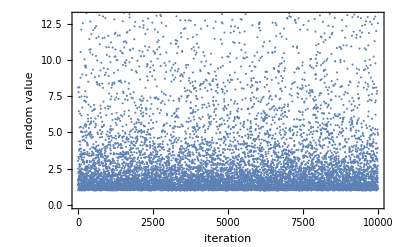

```mathematica
n=10000;
rlist=Table[1/Random[],{i,1,n}];
Show[ListPlot[rlist,Frame->True,FrameLabel->{"iteration","random value"}]]
(* If we take an inverse power, we get another nonuniform distribution.  *)
```

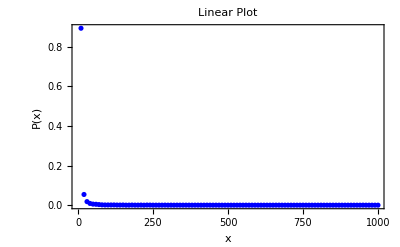

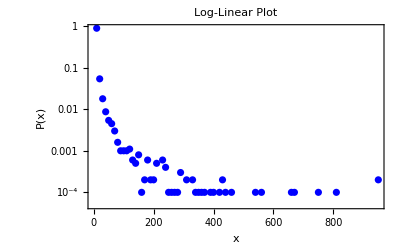

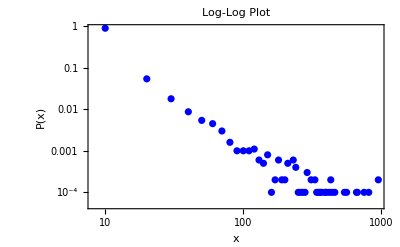

```mathematica
nbin=100;
maxval=1000.;
bins=Table[{i maxval/nbin,0},{i,1,nbin}];
Do[
rval=rlist[[i]];  (*pick a random value to bin *)
Do[
If[rval<bins[[j,1]],  (* if that random value is smaller than the current bin,*)
bins[[j,2]]+=1./n;  (* put it into the bin *)
Break[] (* once we found its bin, stop! *)
];
,{j,1,nbin}];  (* search over all bins *)

,{i,1,n}]; (* check all numbers *)
p1=ListPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotRange->All,PlotLabel->"Linear Plot"]  (* plot the data *)
p2=ListLogPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotRange->All,PlotLabel->"Log-Linear Plot"]  
p3=ListLogLogPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotRange->All,PlotLabel->"Log-Log Plot"]  (* plot the data *)

(* binning is useless for this distribution!  Almost everything is close to zero, except for some rare points that are huge.  *)
```

{A→8243.64,B→-3.96541}

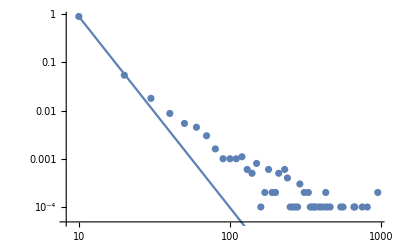

{A→1.8346,B→-1.81308}

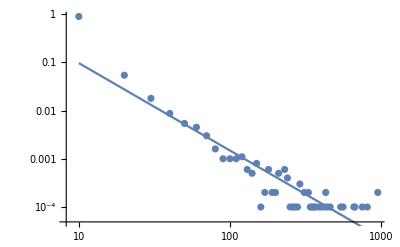

```mathematica
(* trying to fit the data doesn't work very well at all.  Only the first couple of points are included in the fit.  *)

MediocreFit1=FindFit[DeleteCases[bins,{x_,0}],A x^B,{A,B},x]
LogLogPlot[A x^B/.%,{x,10,1000}];
ListLogLogPlot[bins];
Show[%,%%]


(* that's because most of the data is very small.  If we fit the logarithm of the data, we pick up the large x values.  However, we cease to fit the small points! *)
MediocreFit2=FindFit[Log[DeleteCases[bins,{x_,0}]],A+B x,{A,B},x]
LogLogPlot[Exp[A+B Log[x]]/.%,{x,10,1000}];
ListLogLogPlot[bins];
Show[%,%%]
```

```mathematica
Print["KS-test had statistic:  ",KolmogorovSmirnovTest[rlist,ParetoDistribution[1,-B/.MediocreFit1],{"PValue","ShortTestConclusion"}]," using linear values with linear binning"]
Print["KS-test had statistic:  ",KolmogorovSmirnovTest[rlist,ParetoDistribution[1,-B/.MediocreFit2],{"PValue","ShortTestConclusion"}]," using logged values with linear binning"]
```

General::munfl: Exp[-4454.35] is too small to represent as a normalized machine number; precision may be lost.

KS-test had statistic:  {0.,Reject} using linear values with linear binning

General::munfl: Exp[-936.] is too small to represent as a normalized machine number; precision may be lost.

KS-test had statistic:  {0.,Reject} using logged values with linear binning

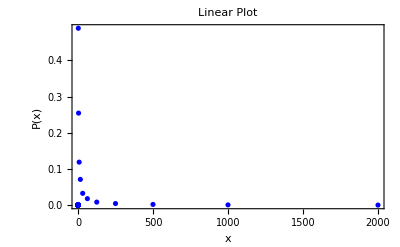

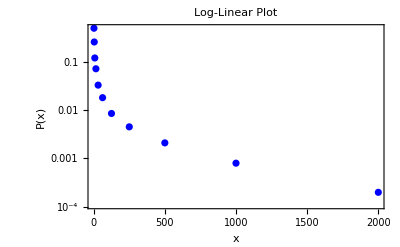

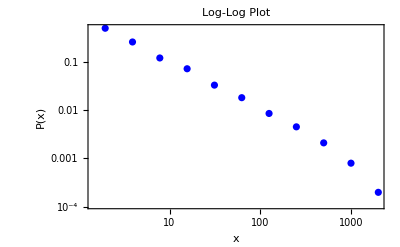

```mathematica
(* We can overcome this by recognizing the data is broadly distributed:  very few points are in any linear bin, except for the first couple.  We should have small bins for small values and large bins to cluster large values together.  *)


nbin=100;
maxval=2000.;
bins=Table[{2^(-nbin+i)maxval,0},{i,1,nbin}];
(* this picks bins that grow exponentially in size.  This means the rare huge points will be grouped together more efficiently.  *)
Do[
rval=rlist[[i]];  (*pick a random value to bin *)
Do[
If[rval<bins[[j,1]],  (* if that random value is smaller than the current bin,*)
bins[[j,2]]+=1./n;  (* put it into the bin *)
Break[] (* once we found its bin, stop! *)
];
,{j,1,nbin}];  (* search over all bins *)

,{i,1,n}]; (* check all numbers *)
p1=ListPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotRange->All,PlotLabel->"Linear Plot"]  (* plot the data *)
p2=ListLogPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotRange->All,PlotLabel->"Log-Linear Plot"]  
p3=ListLogLogPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotRange->All,PlotLabel->"Log-Log Plot",PlotRange->All]  

(* The Linear and Log-Linear plots don't look useful, but the Log-Log plot seems to suggest a power-law tail.  The distribution is nonmonotonic, because we have too-high resolution for small values.    *)
```

{A→0.187433,B→-1.06276}

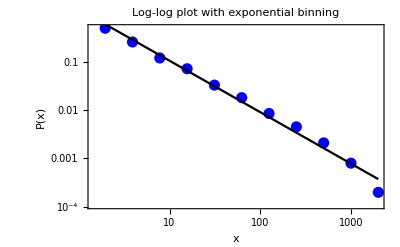

```mathematica
bestFit=FindFit[Log[DeleteCases[bins,{x_,0}]],A+B x,{A,B},x]
LogLogPlot[Exp[A +B Log[x]]/.%,{x,1,2000},PlotStyle->Black];
ListLogLogPlot[bins,PlotStyle->{Blue,PointSize[.02]}];
Show[%,%%,Frame->True,Axes->False,FrameLabel->{"x","P(x)"},PlotLabel->"Log-log plot with exponential binning"]
```

```mathematica
(* Sometimes the fit will be accepted, sometimes rejected *)
Print["KS-test had statistic:  ",KolmogorovSmirnovTest[rlist,ParetoDistribution[1,-B/.bestFit],{"PValue","ShortTestConclusion"}]," using exponential binning"]
```

KS-test had statistic:  {1.0251×10^-6,Reject} using exponential binning

```mathematica
(* We failed because we were too confident about our value of the exponent (B).  We should take into account we have some confidence interval around the best fit value.  FindFit doesn't tell us this, but a related NonlinearModelFit will! *)
CIs=NonlinearModelFit[DeleteCases[bins,{x_,0}],A x^B,{A,B},x]["ParameterConfidenceIntervals"]
```

{{0.905511,0.96734},{-1.00128,-0.937297}}

```mathematica
Print["KS-test had statistic:  ",KolmogorovSmirnovTest[rlist,ParetoDistribution[1,-CIs[[2,1]]/.bestFit],{"PValue","ShortTestConclusion"}]," with the upper bound on the confidence interval"]

Print["KS-test had statistic:  ",KolmogorovSmirnovTest[rlist,ParetoDistribution[1,-CIs[[2,2]]/.bestFit],{"PValue","ShortTestConclusion"}]," with the lower bound on the confidence interval"]
```

KS-test had statistic:  {0.177674,Do not reject} with the upper bound on the confidence interval

KS-test had statistic:  {2.87494×10^-7,Reject} with the lower bound on the confidence interval